```mathematica
{m,n}
```

{480,360}

## PCA Denoising

```mathematica
cwd=NotebookDirectory[];
{m,n}=Import[cwd<>"snowy_owl.jpg","ImageSize"];
original=Import[cwd<>"snowy_owl.jpg"];
noisey=ImageEffect[original,{"GaussianNoise",0.1}]
pxl=N[Flatten[ImageData[noisey],1]];
mean=Mean[pxl];
pxlCtr=#-mean&/@pxl;
(*RGB channels*)
R=ArrayReshape[pxlCtr[[All,1]],{m,n}];G=ArrayReshape[pxlCtr[[All,2]],{m,n}];B=ArrayReshape[pxlCtr[[All,3]],{m,n}];
```

-Graphics-

## PCA and reconstruction

```mathematica
Clear[recon];
(*Reconstruction single channel*)
recon[channel_,nPC_]:=Module[{u,s,v,picrecon},
(*SVD*){u,s,v}=SingularValueDecomposition[channel];
(*Reconstruction using nPC columns*)picrecon=u[[All,;;nPC]].s[[;;nPC,;;nPC]].Transpose[v[[All,;;nPC]]];
picrecon]
(*Reconstruct 3 channels*)
reconRGB[nPC_]:=ArrayReshape[Transpose[Flatten/@{recon[R,nPC],recon[G,nPC],recon[B,nPC]}],{n,m,3}]
rgbPlot[plot_]:=ArrayPlot[ArrayReshape[plot,{n,m,3}],ColorFunction->Function[p,RGBColor[p[[1]],p[[2]],p[[3]]]],ColorFunctionScaling->True]
```

## Plotting

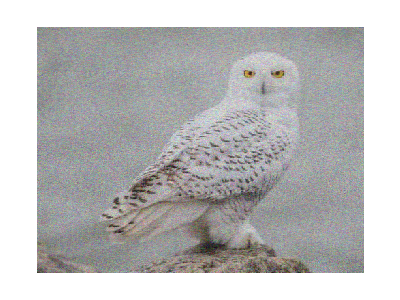

```mathematica
rgbPlot[reconRGB[#]]&/@{100}
```